```mathematica
cLetraj[x0_,tf_]  :=
(*Finds the fullspace trajectory with initial point x0 for a time tf*)Module[ {r1=28,r2=0,b=8/3,e=1/10,s=10,tf1=tf,xi=x0//Flatten,traj,v,x,eqns,xde,ic,sol,x1,x2,y1,y2,z,t}, 
v[t_]={-s*x1[t]+s*y1[t],-s* x2[t]+s* y2[t],(r1-z[t])*x1[t]-r2* x2[t]-y1[t]-e* y2[t],r2* x1[t]+(r1-z[t])*x2[t]+e* y1[t]-y2[t],-b *z[t]+x1[t]* y1[t]+x2[t]* y2[t]};
	x[t_]={x1[t],x2[t],y1[t],y2[t],z[t]};
	eqns=Table[D[x[t][[i]],t]==v[t][[i]],{i,1,5}];
	xde={x1,x2,y1,y2,z};
ic={x1[0]==xi[[1]],x2[0]==xi[[2]],y1[0]==xi[[3]],y2[0]==xi[[4]],z[0]==xi[[5]]};
	sol=NDSolve[{eqns,ic},xde,{t,0,tf1},MaxSteps->∞]//Flatten;
	traj[t_]=x[t]/.sol;
traj
]
cLeVel[x0_]:=
(*Calculates the full space velocity at the point x0*)
Module[{r1=28,r2=0,b=8/3,e=1/10,s=10,xi=x0//Flatten,v},
v={-s*xi[[1]]+s*xi[[3]],-s*xi[[2]]+s*xi[[4]],(r1-xi[[5]])*xi[[1]]-r2*xi[[2]]-xi[[3]]-e* xi[[4]],r2* xi[[1]]+(r1-xi[[5]])*xi[[2]]+e* xi[[3]]-xi[[4]],-b *xi[[5]]+xi[[1]]*xi[[3]]+xi[[2]]*xi[[4]]};
v
]
cLeRot[x0_,tx_]:=
(*finds the point in the group orbit of x0 in the slice normal to tx*)
Module[{xi=x0//Flatten,ti=tx//Flatten,T={{0,1,0,0,0},{-1,0,0,0,0},{0,0,0,1,0},{0,0,-1,0,0},{0,0,0,0,0}},G,theta,v},
theta=T.{{xi[[1]]},{xi[[2]]},{xi[[3]]},{xi[[4]]},{xi[[5]]}};
theta=theta//Flatten;
theta=(xi.ti)/(theta.ti);
theta=ArcTan[-theta];
G={{Cos[theta],Sin[theta],0,0,0},{-Sin[theta],Cos[theta],0,0,0},{0,0,Cos[theta],Sin[theta],0},{0,0,-Sin[theta],Cos[theta],0},{0,0,0,0,1}};
xi={{xi[[1]]},{xi[[2]]},{xi[[3]]},{xi[[4]]},{xi[[5]]}};
xi=(G.xi)//Flatten;
theta=T.{{xi[[1]]},{xi[[2]]},{xi[[3]]},{xi[[4]]},{xi[[5]]}};
theta=theta//Flatten;
If[theta.ti<0,
xi={-xi[[1]],-xi[[2]],-xi[[3]],-xi[[4]],xi[[5]]};
];
xi
]
cLeRotSlice[x0_,tf_,tx_]:=
(*Finds the reduced space trajectory. Does this by taking the full space trajectory and then rotating it into the slice.*)Module[{xi=x0//Flatten,tfi=tf,ti=tx//Flatten,traj,t,slice},
traj=cLetraj[xi,tfi];
slice[t_]:=cLeRot[traj[t],ti];
slice
]
cLeSliceFind[x0_,tf_,a_]:=(*Finds the normal to a slice where the trajectory through x0 passes through a singularity. The singularity occurs at time tf/2. The method produces two linearly independent vectors and the vector a is used to determine what linear combination of the two vectors you want to use for the normal to the slice.*)Module[{xi=x0//Flatten,tfi=tf,traj,x1,T={{0,1,0,0,0},{-1,0,0,0,0},{0,0,0,1,0},{0,0,-1,0,0},{0,0,0,0,0}},A,r,s,t},
traj=cLetraj[xi,tfi];
x1=traj[tfi/2];
r=(x1[[1]]^2)+(x1[[2]])^2;
s=x1[[2]]*x1[[3]]-x1[[1]]*x1[[4]];
t=x1[[1]]*x1[[3]]+x1[[2]]*x1[[4]];
A={{s/r,-t/r,0,1,0},{-t/r,-s/r,1,0,0}};
a.A
]
cLevt[slice_,tx_]:=
(*finds v(y).tx along the reduced space trajectory slice*)
Module[{slicei=slice,ti=tx//Flatten,vt,v},
v[t_]:=cLeVel[slicei[t]];
vt[t_]:=v[t].ti;
vt
]
cLeTt[slice_,tx_]:=
(*finds t(y).tx along the reduced space trajectory slice*)Module[{slicei=slice,ti=tx//Flatten,Tt,T={{0,1,0,0,0},{-1,0,0,0,0},{0,0,0,1,0},{0,0,-1,0,0},{0,0,0,0,0}},Tx,Txf,t},
Tx[t_]:=T.{{slicei[t][[1]]},{slicei[t][[2]]},{slicei[t][[3]]},{slicei[t][[4]]},{slicei[t][[5]]}};
Txf[t_]:=Tx[t]//Flatten;
Tt[t_]:=Txf[t].ti;
Tt
]
cLeDtheta[slice_,tx_]:=
(*finds Dtheta along the reduced space trajectory slice*)Module[{slicei=slice,ti=tx//Flatten,dtheta,vt,Tt},
vt=cLevt[slicei,ti];
Tt=cLeTt[slicei,ti];
dtheta[t_]:=vt[t]/Tt[t];
dtheta
]
cLeSlice[x0_,tf_,tx_]:=
(*Calculates the reduced space trajectory in with initial point x0 for a time tf. It does this for the slice normal to tx. It does this by solving the differential equations in the reduced space*)
Module[{r1=28,r2=0,b=8/3,e=1/10,s=10,xi=x0//Flatten,tfi=tf,ti=tx//Flatten,theta,G,dtheta,v,T={{0,1,0,0,0},{-1,0,0,0,0},{0,0,0,1,0},{0,0,-1,0,0},{0,0,0,0,0}},x,Tx,u,eqns,xde,x1,x2,y1,y2,z,ic,sol,traj,t,Tt},
theta=T.{{xi[[1]]},{xi[[2]]},{xi[[3]]},{xi[[4]]},{xi[[5]]}};
theta=theta//Flatten;
If[theta.ti==0,
theta=Pi/2;,
theta=(xi.ti)/(theta.ti);
theta=ArcTan[-theta];
];
G={{Cos[theta],Sin[theta],0,0,0},{-Sin[theta],Cos[theta],0,0,0},{0,0,Cos[theta],Sin[theta],0},{0,0,-Sin[theta],Cos[theta],0},{0,0,0,0,1}};
xi={{xi[[1]]},{xi[[2]]},{xi[[3]]},{xi[[4]]},{xi[[5]]}};
xi=(G.xi)//Flatten;
x[t_]={x1[t],x2[t],y1[t],y2[t],z[t]};
v[t_]={-s*x1[t]+s*y1[t],-s* x2[t]+s* y2[t],(r1-z[t])*x1[t]-r2* x2[t]-y1[t]-e* y2[t],r2* x1[t]+(r1-z[t])*x2[t]+e* y1[t]-y2[t],-b *z[t]+x1[t]* y1[t]+x2[t]* y2[t]};
Tx[t_]=(T.{{x1[t]},{x2[t]},{y1[t]},{y2[t]},{z[t]}})//Flatten;
Tt[t_]=Tx[t].ti;
dtheta[t_]=(v[t].ti)/(Tt[t]);
u[t_]=v[t]-dtheta[t]*Tx[t];
x[t_]={x1[t],x2[t],y1[t],y2[t],z[t]};
eqns=Table[D[x[t][[i]],t]==u[t][[i]],{i,1,5}];
xde={x1,x2,y1,y2,z};
ic={x1[0]==xi[[1]],x2[0]==xi[[2]],y1[0]==xi[[3]],y2[0]==xi[[4]],z[0]==xi[[5]]};
sol=NDSolve[{eqns,ic},xde,{t,0,tfi},MaxSteps->∞]//Flatten;
traj[t_]=x[t]/.sol;
traj
]
```

```mathematica
(*Plot of a dtheta of the reduced space trajectory beginning at x0 that goes through a singularity at time tf/2*)
x0={-1.22,3.212,-4.31,1.11,4};
tf=0.2;
tx=cLeSliceFind[x0,tf,{0.4,0.12}];
slice=cLeRotSlice[x0,tf,tx];
dtheta=cLeDtheta[slice,tx];
p=Plot[dtheta[s],{s,0,tf},PlotRange->{{0,0.2},{0,40}},TicksStyle-> Larger,Ticks->{{0,0.05,0.10,0.15,0.2},{0,10,20,30,40}},ImagePadding->{{100,20},{40,25}},PlotRangeClipping->False,PlotStyle->{Blue}];

(*Next three plots are of a dtheta of the reduced space trajectory with initial point x0+dx*)
dx={0.001,0,0,0,0};
x1=x0+dx;
slice1=cLeRotSlice[x1,tf,tx];
dtheta1=cLeDtheta[slice1,tx];
p1=Plot[dtheta1[s],{s,0,tf},PlotRange->{{0,0.2},{0,40}},TicksStyle-> Larger,Ticks->{{0,0.05,0.10,0.15,0.2},{0,10,20,30,40}},ImagePadding->{{100,20},{40,25}},PlotRangeClipping->False,PlotStyle->{Blue}];

dx={0.01,0,0,0,0};
x2=x0+dx;
slice2=cLeRotSlice[x2,tf,tx];
dtheta2=cLeDtheta[slice2,tx];
p2=Plot[dtheta2[s],{s,0,tf},PlotRange->{{0,0.2},{0,40}},TicksStyle-> Larger,Ticks->{{0,0.05,0.10,0.15,0.2},{0,10,20,30,40}},ImagePadding->{{100,20},{40,25}},PlotRangeClipping->False,PlotStyle->{Blue}];

dx={0.1,0,0,0,0};
x3=x0+dx;
slice3=cLeRotSlice[x3,tf,tx];
dtheta3=cLeDtheta[slice3,tx];
p3=Plot[dtheta3[s],{s,0,tf},PlotRange->{{0,0.2},{0,40}},TicksStyle-> Larger,Ticks->{{0,0.05,0.10,0.15,0.2},{0,10,20,30,40}},ImagePadding->{{100,20},{40,25}},PlotRangeClipping->False,PlotStyle->{Blue}];
```

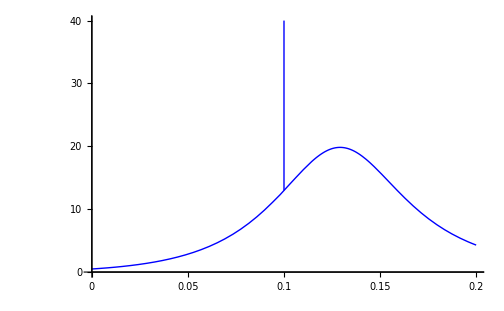

```mathematica
l=Graphics[{Blue,Line[{{0.1,13},{0.1,40}}]}];Show[p,Graphics[Text[Style["τ",Large],{0.1,-5}]],Graphics[Text[Style[OverDot["θ"],Large],{-0.016,20}]],l,Graphics[Arrow[{{0,0},{0,44}}]],Graphics[Arrow[{{0,0},{0.21,0}}]],Graphics[Text[Style["(a)",Large],{-0.04,20}]]]
```

```mathematica
Show[p1,Graphics[Text[Style["τ",Large],{0.1,-5}]],Graphics[Text[Style[OverDot["θ"],Large],{-0.016,20}]],Graphics[Arrow[{{0,0},{0,44}}]],Graphics[Arrow[{{0,0},{0.21,0}}]],Graphics[Text[Style["(b)",Large],{-0.04,20}]]]
```

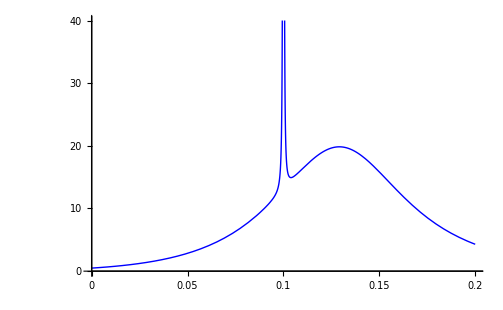

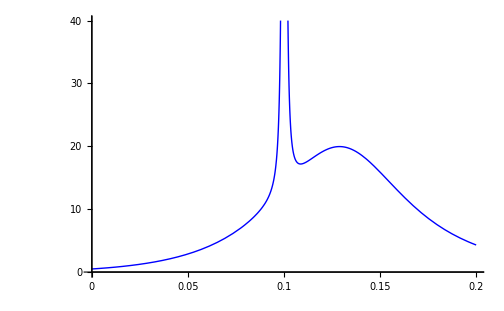

```mathematica
Show[p2,Graphics[Text[Style["τ",Large],{0.1,-5}]],Graphics[Text[Style[OverDot["θ"],Large],{-0.016,20}]],Graphics[Arrow[{{0,0},{0,44}}]],Graphics[Arrow[{{0,0},{0.21,0}}]],Graphics[Text[Style["(c)",Large],{-0.04,20}]]]
```

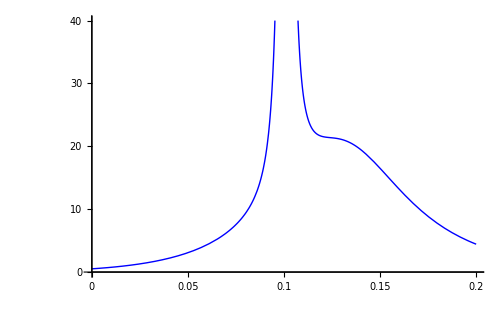

```mathematica
Show[p3,Graphics[Text[Style["τ",Large],{0.1,-5}]],Graphics[Text[Style[OverDot["θ"],Large],{-0.016,20}]],Graphics[Arrow[{{0,0},{0,44}}]],Graphics[Arrow[{{0,0},{0.21,0}}]],Graphics[Text[Style["(d)",Large],{-0.04,20}]]]
```